# Phase portraits (figures 3 and 4)

## Author: Charlie Brummitt

## Preliminaries

Set the working directory to the notebook directory:

```mathematica
SetDirectory[NotebookDirectory[]];
```

The path in which to save figures:

```mathematica
figuresDirectory=FileNameJoin[{ParentDirectory@NotebookDirectory[],"figures"}];
```

Import strategiesThatCouldBeBestResponses and probSuccess:

```mathematica
Get["set_strategies_that_could_be_best_response.wl"];
```

## Figure 3

We fix the exogenous parameters α=0.1,β=0.4 and iterate over F from 0 to 1 in steps of 10^-4. For each value of F, we compute the best response from equation 4 and the ODE from equation (2b).

### compute best responses

```mathematica
ClearAll[ϵ];
```

```mathematica
Module[{utility,β=.4,α=0.1,strategies,br,probSuccess},
utility[{mInput_,τInput_},FInput_,{αInput_,βInput_}]:=Probability[S≥τInput,S\[Distributed]BinomialDistribution[mInput,FInput]] τInput^βInput-αInput mInput;

bestResponsesα0p1β0p4=
ParallelTable[
strategies=strategiesThatCouldBeBestResponses[{α,β},F];
br=First[MaximalBy[strategies,utility[#,F,{α,β}]&]];
probSuccess=If[br=!={0,0},Probability[S≥br⟦2⟧,S\[Distributed]BinomialDistribution[br⟦1⟧,F]],0];

<|
"α"->α,
"β"->β,
"F"->F,
"bestResponse"->br,
"Fdot"-> (probSuccess-F (1+ϵ))*Boole[br[[2]]>0]
|>
,{F,0,1,0.0001}];
]//AbsoluteTiming
```

{882.,Null}

This took 14.7 minutes to compute:

```mathematica
UnitConvert[Quantity[882.,"Seconds"],"Minutes"]
```

14.7 min

#### save the best responses to a file in the folder simulated_data

```mathematica
bestResponsesα0p1β0p4>>(FileNameJoin[{"simulated_data","bestResponses_alpha0p1_beta0p4"}])
```

#### load the best responses from the hard disk

```mathematica
bestResponsesα0p1β0p4=(<<(FileNameJoin[{"simulated_data","bestResponses_alpha0p1_beta0p4"}]));
```

## compute ODEs

Now we split the best responses by the best response (m^*,τ^*) and by the sign of d F/d t :

```mathematica
splitBestResponses=Block[{ϵ=10^-3.},
SplitBy[bestResponsesα0p1β0p4,
{#bestResponse, Sign[#Fdot]}&]
];
```

This SplitBy results in a list of lists, each one corresponding to one curve in the figure.

Next we compute the ODE for each of these curves and d F/d t at the midpoint of the curve:

```mathematica
ODEs=Block[{ϵ=10^-3.,bestResponses=bestResponsesα0p1β0p4},
((Association@
{"ODE"->(P-F (1+ϵ)) * Boole[τ>0]
/.{P->Probability[S≥τ,S\[Distributed]BinomialDistribution[m,F]]}
/.{m->#1["bestResponse"][[1]],τ->#1["bestResponse"][[2]]},
"Fiterator"->{F,#1["F"],#2["F"]},
"Fmidpoint"->(#1["F"]+#2["F"])/2.0,
"bestResponse"->#1["bestResponse"],
"FdotMidPoint"->#Fdot/.{F-> (#1["F"]+#2["F"])/2 }}&)@@@(Drop[#,{2,-2}]&/@
Select[
splitBestResponses,
Length[#]≥2&]))];
```

### Make figure 3

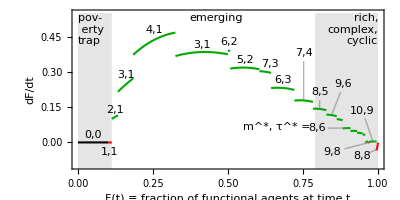

```mathematica
Block[{ϵ=.001,increasingColor=Darker@Green,decreasingColor=Red,stationaryColor=Black,fontOffset=6,fontMultiplier=15,fontExponent=1,plots,fontSize=10,ODEs=ODEs,font="Arial",imageSize= 3.41/3.44 {8.7 *72/2.54},aspectRatio=.5,displacement,callout,bestResponses=bestResponsesα0p1β0p4,styleLabel,createLabel,plotRange,columnSpacings=.3,spaceBetweenMτ=Spacer[1.2]},

plots=(Plot[#ODE,#Fiterator,

PlotStyle->{Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,stationaryColor],AbsoluteThickness[1.5]}

]&)/@ODEs;

styleLabel[lbl_,width_]:=Style[lbl,{FontFamily->"Times"}];

displacement[br_,FdotMidPoint_]:={0,0.02}
+
Which[
br[[1]]≥8||br=={7,3},{0,(.05+br[[2]]*.01) Sign[FdotMidPoint]}
,True,{0,0}
]
+If[br=={9,6},{0,.07},0]
+If[br=={10,7},{-.05,-.2},0]
;

callout[label_,pos_,pointPos_]:={Inset[label,pos],Line[pos,pointPos]};
createLabel=Module[{positionArrowhead,positionLabel,displaceLabelPosition,d=.032},

If[
(* Show labels for these portions of the ODE *)
#Fmidpoint≤.85||(#bestResponse=={9,8}&&#FdotMidPoint<0)||#bestResponse=={8,8}||#bestResponse=={8,6}||(#bestResponse=={10,9}&&#FdotMidPoint>0),

positionArrowhead={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};
positionLabel={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};

displaceLabelPosition={0,0};
Which[
#bestResponse=={0,0},displaceLabelPosition+={0,d};,
#bestResponse=={1,1},displaceLabelPosition+={0,-.04};,
#bestResponse=={2,1}||#bestResponse=={5,2},displaceLabelPosition+={0,d};,
#bestResponse=={3,1}&&#Fmidpoint<.2,displaceLabelPosition+={0,.042};,
#bestResponse=={3,1}&&#Fmidpoint>.2,displaceLabelPosition+={0,d};,
#bestResponse=={4,1},displaceLabelPosition={0,.04};,
#bestResponse=={7,3},displaceLabelPosition={0.015,.035};,
#bestResponse=={6,2},displaceLabelPosition={0.0,.035};,
#bestResponse=={6,3},displaceLabelPosition={0 0.015,.035};,
#bestResponse=={7,4},displaceLabelPosition={0,.2};,
#bestResponse=={8,5},displaceLabelPosition={0,.07};,
#bestResponse=={9,6},displaceLabelPosition={.04,.13};,
#bestResponse=={10,7},displaceLabelPosition={0,.15};,
#bestResponse=={8,6},displaceLabelPosition={-.1,0};,
#bestResponse=={9,7},displaceLabelPosition={0,.1};,
#bestResponse=={10,8},displaceLabelPosition={0,.15};,
#bestResponse=={11,9},displaceLabelPosition={0,.08};,
#bestResponse=={8,7},displaceLabelPosition={-.1,0};,
#bestResponse=={9,8},displaceLabelPosition={-.12,-0.04};,
#bestResponse=={10,9}&&#FdotMidPoint<0,displaceLabelPosition={-.05,-0.1};,
#bestResponse=={10,9}&&#FdotMidPoint>0,displaceLabelPosition={-.035,0.13};,
#bestResponse=={10,10}&&#FdotMidPoint<0,displaceLabelPosition={-.06,-0.15};,
#bestResponse=={8,8}&&#FdotMidPoint<0,displaceLabelPosition={-.05,-0.03};

];

positionLabel+=displaceLabelPosition;

{

Inset[
Row[
Style[#,{FontFamily->font}]&/@
Join[
If[False,
{
Style["m^*",Gray],Style[",",Gray],
spaceBetweenMτ,
Style["τ^*",Gray],
spaceBetweenMτ,
 Style["=",Gray],
spaceBetweenMτ
}
,
{}],
{
Style[#["bestResponse"]⟦1⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],Style[",",Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],
spaceBetweenMτ,
Style[#["bestResponse"]⟦2⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]]
}]
],
positionLabel]

,
If[Norm[positionLabel-positionArrowhead]>.05,
{Gray,Opacity[.6],Line[
{positionLabel+.033 Normalize[positionArrowhead-positionLabel]
+If[#bestResponse=={9,8},.01 Normalize[positionArrowhead-positionLabel],0]
+If[#bestResponse=={8,6},.004 Normalize[positionArrowhead-positionLabel],0]
,positionArrowhead}]}
,
Nothing
]
}
,
Nothing
]
]

&;

plotRange={-.1,.55};

Show[
plots,
FrameLabel->(Style[#,{FontFamily->font,FontSize->fontSize}]&/@{"F(t) ≡ fraction of functional agents at time t","dF/dt"}),
ImageSize->imageSize,PlotRange->plotRange,Filling->Axis,PlotRangeClipping->True,PlotRangePadding->{{0.0,0.005},{0,0}},FrameTicksStyle->Directive[FontFamily->font,Gray],ImagePadding->{{All,All},{All,1}},
Prolog->
{
{{Opacity[.1],Rectangle[{0,-1},{SelectFirst[bestResponses,Chop[#["Fdot"]/."L"->L]>0&]["F"],plotRange⟦2⟧}]}},
{{Opacity[.1],Rectangle[{.79,-1},{1,plotRange⟦2⟧}]}}
},
AspectRatio->aspectRatio,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
Epilog->Join[createLabel/@ODEs,{Inset[
Column[{
Style["pov-",{FontFamily->font,FontSize->fontSize}],Style[" erty",{FontFamily->font,FontSize->fontSize}],
Style["trap",{FontFamily->font,FontSize->fontSize}]
},Alignment->Left,Spacings->columnSpacings]
,{0,.55},{-1.25,1}],
Inset[
Column[
{Style["rich,",{FontFamily->font,FontSize->fontSize}],
Style["complex,",{FontFamily->font,FontSize->fontSize}],
Style["cyclic",{FontFamily->font,FontSize->fontSize}]}
,Spacings->columnSpacings,Alignment->Center]
,{1,.55},{1.,1}],
Inset[
Column[
{Style["emerging",{FontFamily->font,FontSize->fontSize}]}
,Spacings->columnSpacings,Alignment->Center]
,{0.4613508326896292,.55},{0,1}],
Inset[
Row[Style[#,{FontFamily->font}]&/@{
Style["m^*",FontSize->fontSize,Black],
Style[", ",FontSize->fontSize,Black],
Style["τ^*",FontSize->fontSize,Black],
Style[" = ",FontSize->fontSize,Black]
}]
,{.662,.066}
]
}]
]
]
Export[FileNameJoin[{figuresDirectory,"figure3_revision.pdf"}],%];
```

## Figure 4

Here, agents use a strategy that requires s=2 more inputs than they would have chosen given the reliability F(t) of their potential inputs: they use the strategy (m^*+2,τ^*+2), where (m^*,τ^*) is the best response.

### compute best response with s=2 extra inputs

```mathematica
Module[{s=2,ϵ=.001},
bestResponsesα0p1β0p4With2ExtraInputs=
<|"α"->#α,"β"->#β,"F"->#F,"bestResponse"->#bestResponse+{s,s},
"Fdot"->
(probSuccess[#bestResponse+{s,s},#F]-#F (1+ϵ)) Boole[#bestResponse[[2]]+s>0]
|>&/@bestResponsesα0p1β0p4;
]
```

```mathematica
ODEsα0p1β0p4With2ExtraInputs=Module[{s=2,ϵ=0.001,bestResponses=bestResponsesα0p1β0p4With2ExtraInputs},
((Association@
{
"ODE"->(P-F (1+ϵ)) * Boole[τ>0]
/.{P->Probability[S≥τ,S\[Distributed]BinomialDistribution[m,F]]}
/.{m->#1["bestResponse"][[1]],τ->#1["bestResponse"][[2]]}
,
"Fiterator"->{F,#1["F"],#2["F"]},
"Fmidpoint"->(#1["F"]+#2["F"])/2.0,
"bestResponse"->#1["bestResponse"],
"FdotMidPoint"->((#Fdot/.{F-> (#1["F"]+#2["F"])/2}))}&)@@@(Drop[#,{2,-2}]&/@Select[SplitBy[bestResponses,{#bestResponse,Sign[#Fdot]}&],Length[#]≥2&]))];
```

### plot figure 4

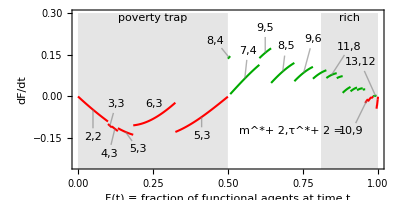

```mathematica
Module[{increasingColor=Darker@Green,decreasingColor=Red,stationaryColor=Black,fontOffset=6,fontMultiplier=15,fontExponent=1,plots,fontSize=10,ODEs=ODEsα0p1β0p4With2ExtraInputs,font="Arial",imageSize= 3.41/3.44 {8.7 *72/2.54},aspectRatio=.5,displacement,callout,styleLabel,createLabel,plotRange,columnSpacings=.2,povertyTrapRightEndpoint,richLeftEndpoint,shiftmτLabel={-.02,.03},spaceBetweenMτ=Spacer[1.2]},

plots=(Plot[#ODE,#Fiterator,

PlotStyle->{Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,stationaryColor],AbsoluteThickness[1.5]}

]&)/@ODEs;

povertyTrapRightEndpoint=SelectFirst[ODEs,#FdotMidPoint>0&]["Fiterator"]⟦2⟧;
richLeftEndpoint=.81(*Select[Reverse[ODEs],#FdotMidPoint>0&]⟦4⟧["Fiterator"]⟦2⟧*);

styleLabel[lbl_,width_]:=Style[lbl,{FontFamily->"Times"}];

displacement[br_,FdotMidPoint_]:={0,0.02}
+
Which[
br[[1]]≥8||br=={7,3},{0,(.05+br[[2]]*.01) Sign[FdotMidPoint]}
,True,{0,0}
]
+If[br=={9,6},{0,.07},0]
+If[br=={10,7},{-.05,-.2},0]
;

callout[label_,pos_,pointPos_]:={Inset[label,pos],Line[pos,pointPos]};
createLabel=Module[{positionArrowhead,positionLabel,displaceLabelPosition,d=.032},

If[
(* Show labels for these portions of the ODE *)
(#Fmidpoint≤.85||#bestResponse=={10,9}||(#bestResponse=={13,12}&&#FdotMidPoint>0))&&Not[#bestResponse=={10,7}],


positionArrowhead={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};
positionLabel={#["Fmidpoint"],#["ODE"]/.F->#["Fmidpoint"]};

displaceLabelPosition={0,0};
displaceLabelPosition+=If[#FdotMidPoint>0,{0,.05},{0,-.05}];
displaceLabelPosition+=
Which[
#bestResponse=={2,2},{0,-.05},
#bestResponse=={3,3},{.02,.128},
#bestResponse=={4,3},{-.02,-.04},
#bestResponse=={5,3}&&#Fmidpoint<.3,{.04,-.01},
#bestResponse=={5,3}&&#Fmidpoint>.3,{0,-.02}(*{0,.15}*),
#bestResponse=={6,3},{0,.10},
#bestResponse=={7,4}&&#FdotMidPoint<0,{0,-.05},
#bestResponse=={7,4}&&#FdotMidPoint>0,{.01,.05},
#bestResponse=={8,4},{-.045,.01},
#bestResponse=={8,5},{0.01,Sign[#FdotMidPoint] .04},
#bestResponse=={9,5},{0,.04},
#bestResponse=={9,6}&&#FdotMidPoint>0,{.03,.07},
#bestResponse=={9,6}&&#FdotMidPoint<0,{.05,-.05},
#bestResponse=={13,12}&&#FdotMidPoint>0,{-.05,0.07},
#bestResponse=={10,9}&&#FdotMidPoint<0,{-.05,-0.06},
#bestResponse=={11,8},{.06,.05},
True,{0,0}
];

positionLabel+=displaceLabelPosition;

{
Inset[
Row[
Style[#,{FontFamily->font}]&/@
Join[
If[False,
{
Style["m^*",Gray],
Style[",",Gray],
Style["τ^*",Gray],
Style["= ",Gray]
}
,
{}],
{
Style[#["bestResponse"]⟦1⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],Style[",",Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]],
spaceBetweenMτ,
Style[#["bestResponse"]⟦2⟧,Which[#FdotMidPoint>0,increasingColor,#FdotMidPoint<0,decreasingColor,True,Black]]
}]
],
positionLabel]

,
(* whether to show a gray line *)
If[Norm[positionLabel-positionArrowhead]>.06,
{Gray,Opacity[.6],Line[
{positionLabel+.033 Normalize[positionArrowhead-positionLabel]
,positionArrowhead}]}
,
Nothing
]
}
,
Nothing

]

]&;
plotRange={-.25,.3};

Show[
plots
,FrameLabel->(Style[#,{FontFamily->font,FontSize->fontSize}]&/@{"F(t) ≡ fraction of functional agents at time t","dF/dt"(*"Ḟ ≡ dF/dt"*)}),
ImageSize->imageSize,PlotRange->plotRange,Filling->Axis,PlotRangeClipping->True,PlotRangePadding->{{0.0,0.003},{0,0}},FrameTicksStyle->Directive[FontFamily->font,Gray],
Prolog->
{
{{Opacity[.1],Rectangle[{0,-1},{povertyTrapRightEndpoint,plotRange⟦2⟧}]}},
{{Opacity[.1],Rectangle[{richLeftEndpoint,-1},{1,plotRange⟦2⟧}]}}
},
AspectRatio->aspectRatio,Frame->True,
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
Epilog->Join[createLabel/@ODEs,{Inset[
Column[{
Style["poverty trap",{FontFamily->font,FontSize->fontSize}]
},Alignment->Center,Spacings->columnSpacings]
,{povertyTrapRightEndpoint/2,(*-0.18*)plotRange[[2]]},{0,1.2}],
Inset[
Column[
{Style["rich",{FontFamily->font,FontSize->fontSize}]}
,Spacings->columnSpacings,Alignment->Center]
,{(1+.81)/2(*1*),plotRange[[2]]},{0,1.2}],
Inset[
Row[Style[#,{FontFamily->font,Black}]&/@{
Style["m^*+ 2",FontSize->fontSize],Style[",",FontSize->fontSize],
spaceBetweenMτ,
Style["τ^*+ 2",FontSize->fontSize],
Style[" = ",FontSize->fontSize]
}]
,{.73,-.155}+shiftmτLabel
]
}]
]
]
Export[FileNameJoin[{figuresDirectory,"figure4_revision.pdf"}],%];
```